```mathematica
fs=Table[n!,{n,100}];
```

```mathematica
Through[{Last,Max}[fs]]
```

{93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000,93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000}

{15,19,10,10,14,19,7,14,20,30}

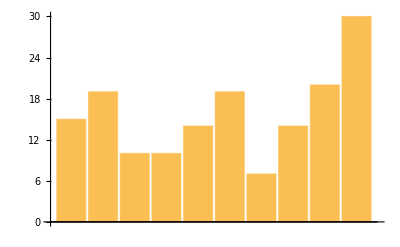

```mathematica
DigitCount[Max[fs]]
BarChart[%]
```

```mathematica
Total@DigitCount[Max[fs]]
IntegerLength[100!]
```

158

158

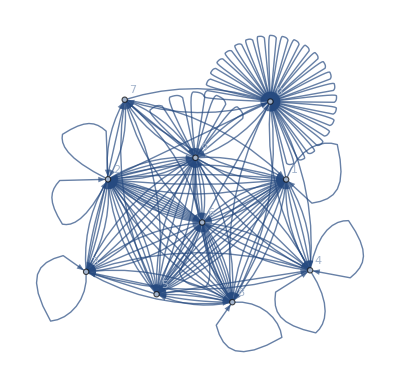

```mathematica
IntegerDigits[100!];
{Most[%],Rest[%]};
Riffle[%[[1]],%[[2]]];
Partition[%,2];
#[[1]]->#[[2]]&/@%;
Graph[%,VertexLabels->"Name"]
```